```mathematica
Solve[p^6-1==0,p]
```

{{p→-1},{p→1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^5+p^4+p^3+p^2+p+1==0,p]
```

{{p→-1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^5-p^4+p^3-p^2+p-1==0,p]
```

{{p→1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^4+p^3-p-1==0,p]
```

{{p→-1},{p→1},{p→-(-1)^(1/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^4-p^3+p-1==0,p]
```

{{p→-1},{p→1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}}

```mathematica
Solve[p^4+p^2+1==0,p]
```

{{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^3+2 p^2+2p+1==0,p]
```

{{p→-1},{p→-(-1)^(1/3)},{p→(-1)^(2/3)}}

```mathematica
Solve[p^3-2 p^2+2p-1==0,p]
```

{{p→1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}}

```mathematica
Solve[p^3+1==0,p]
```

{{p→-1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}}

```mathematica
Solve[p^2-p+1==0,p]
```

{{p→(-1)^(1/3)},{p→-(-1)^(2/3)}}

```mathematica
{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}
```

{1-p+p^2==0,1+p^3==0,-1+2 p-2 p^2+p^3==0,1+2 p+2 p^2+p^3==0,1+p^2+p^4==0,-1+p-p^3+p^4==0,-1-p+p^3+p^4==0,-1+p-p^2+p^3-p^4+p^5==0,1+p+p^2+p^3+p^4+p^5==0,-1+p^6==0}

```mathematica
Table[Solve[i,p],{i,{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}}]
```

{{{p→(-1)^(1/3)},{p→-(-1)^(2/3)}},{{p→-1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}},{{p→1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}},{{p→-1},{p→-(-1)^(1/3)},{p→(-1)^(2/3)}},{{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}},{{p→-1},{p→1},{p→(-1)^(1/3)},{p→-(-1)^(2/3)}},{{p→-1},{p→1},{p→-(-1)^(1/3)},{p→(-1)^(2/3)}},{{p→1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}},{{p→-1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}},{{p→-1},{p→1},{p→-(-1)^(1/3)},{p→(-1)^(1/3)},{p→-(-1)^(2/3)},{p→(-1)^(2/3)}}}

```mathematica
Table[SolveValues[i,p],{i,{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}}]
```

{{(-1)^(1/3),-(-1)^(2/3)},{-1,(-1)^(1/3),-(-1)^(2/3)},{1,(-1)^(1/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}}

```mathematica
Flatten[Table[SolveValues[i,p],{i,{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}}]]
```

{(-1)^(1/3),-(-1)^(2/3),-1,(-1)^(1/3),-(-1)^(2/3),1,(-1)^(1/3),-(-1)^(2/3),-1,-(-1)^(1/3),(-1)^(2/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-1,1,(-1)^(1/3),-(-1)^(2/3),-1,1,-(-1)^(1/3),(-1)^(2/3),1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-1,1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}

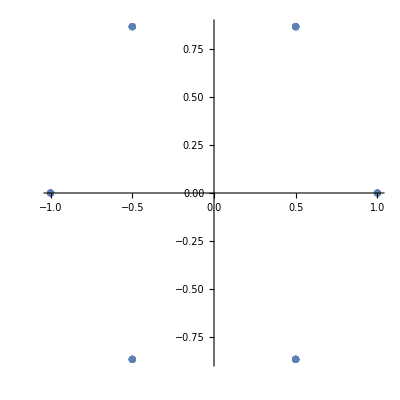

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%15,AspectRatio->1]
```

```mathematica
Union[Flatten[Table[SolveValues[i,p],{i,{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}}]]]
```

{-1,1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}

```mathematica
MinimalPolynomial[#,p]&/@Union[Flatten[Table[SolveValues[i,p],{i,{p^2-p+1==0,p^3+1==0,p^3-2 p^2+2 p-1==0,p^3+2 p^2+2 p+1==0,p^4+p^2+1==0,p^4-p^3+p-1==0,p^4+p^3-p-1==0,p^5-p^4+p^3-p^2+p-1==0,p^5+p^4+p^3+p^2+p+1==0,p^6-1==0}}]]]
```

{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2}

```mathematica
SolveValues[#==0,p]&/@Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]
```

{{-1,-1,-1},{-1,-1,1},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,-1,1},{-1,1,1},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,1},{-1,1,1},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,1},{1,1,1},{1,1,-(-1)^(1/3),(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{1,1,-(-1)^(1/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{1,1,-(-1)^(1/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{1,1,-(-1)^(1/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,(-1)^(1/3),-(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,1,(-1)^(1/3),-(-1)^(2/3)},{1,1,(-1)^(1/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{1,(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),-(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-1,-(-1)^(1/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,1,-(-1)^(1/3),(-1)^(2/3)},{1,1,-(-1)^(1/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),-(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{1,-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)},{-(-1)^(1/3),-(-1)^(1/3),-(-1)^(1/3),(-1)^(2/3),(-1)^(2/3),(-1)^(2/3)}}

```mathematica
Union@Flatten[SolveValues[#==0,p]&/@Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]]
```

{-1,1,-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}

```mathematica
PolynomialRemainder[p^6-1,#,p]&/@Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]
```

{9+24 p+15 p^2,-3+3 p^2,-6-12 p-12 p^2-6 p^3,-2-2 p^3,-2-2 p^3,-6-12 p-12 p^2-6 p^3,-3+3 p^2,-3+3 p^2,0,0,0,0,-6-12 p-12 p^2-6 p^3,0,2+8 p+12 p^2+10 p^3+4 p^4,0,0,2+8 p+12 p^2+10 p^3+4 p^4,-2-2 p^3,0,0,-2-2 p^3,-2-2 p^3,0,-2-2 p^3,0,0,-2-2 p^3,-2-2 p^3,0,-6-12 p-12 p^2-6 p^3,0,2+8 p+12 p^2+10 p^3+4 p^4,0,0,2+8 p+12 p^2+10 p^3+4 p^4,-3+3 p^2,-3+3 p^2,0,0,0,0,-3+3 p^2,9-24 p+15 p^2,-2+2 p^3,-6+12 p-12 p^2+6 p^3,-6+12 p-12 p^2+6 p^3,-2+2 p^3,0,-2+2 p^3,-2+2 p^3,0,0,-2+2 p^3,0,-6+12 p-12 p^2+6 p^3,0,2-8 p+12 p^2-10 p^3+4 p^4,2-8 p+12 p^2-10 p^3+4 p^4,0,0,-6+12 p-12 p^2+6 p^3,0,2-8 p+12 p^2-10 p^3+4 p^4,2-8 p+12 p^2-10 p^3+4 p^4,0,0,-2+2 p^3,-2+2 p^3,0,0,-2+2 p^3,-6-12 p-12 p^2-6 p^3,0,2+8 p+12 p^2+10 p^3+4 p^4,0,0,2+8 p+12 p^2+10 p^3+4 p^4,0,-2+2 p^3,-2+2 p^3,0,0,-2+2 p^3,2+8 p+12 p^2+10 p^3+4 p^4,-2+2 p^3,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,2+8 p+12 p^2+10 p^3+4 p^4,-2+2 p^3,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,-2-2 p^3,0,0,-2-2 p^3,-2-2 p^3,0,0,-6+12 p-12 p^2+6 p^3,0,2-8 p+12 p^2-10 p^3+4 p^4,2-8 p+12 p^2-10 p^3+4 p^4,0,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-2 p^3,2-8 p+12 p^2-10 p^3+4 p^4,-2+p-2 p^2+p^3-2 p^4+p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-2 p^3,2-8 p+12 p^2-10 p^3+4 p^4,-2+p-2 p^2+p^3-2 p^4+p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+p-2 p^2+p^3-2 p^4+p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-2 p^3,0,0,-2-2 p^3,-2-2 p^3,0,0,-6+12 p-12 p^2+6 p^3,0,2-8 p+12 p^2-10 p^3+4 p^4,2-8 p+12 p^2-10 p^3+4 p^4,0,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-2 p^3,2-8 p+12 p^2-10 p^3+4 p^4,-2+p-2 p^2+p^3-2 p^4+p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-2 p^3,2-8 p+12 p^2-10 p^3+4 p^4,-2+p-2 p^2+p^3-2 p^4+p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+3 p-6 p^2+7 p^3-6 p^4+3 p^5,-2+p-2 p^2+p^3-2 p^4+p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-6-12 p-12 p^2-6 p^3,0,2+8 p+12 p^2+10 p^3+4 p^4,0,0,2+8 p+12 p^2+10 p^3+4 p^4,0,-2+2 p^3,-2+2 p^3,0,0,-2+2 p^3,2+8 p+12 p^2+10 p^3+4 p^4,-2+2 p^3,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,0,0,-2-p-2 p^2-p^3-2 p^4-p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2+p-2 p^2+p^3-2 p^4+p^5,-2-p-2 p^2-p^3-2 p^4-p^5,2+8 p+12 p^2+10 p^3+4 p^4,-2+2 p^3,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-p-2 p^2-p^3-2 p^4-p^5,-2-3 p-6 p^2-7 p^3-6 p^4-3 p^5}

```mathematica
Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]]
```

{(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2),(1+p) (1-p+p^2) (1+p+p^2),(-1+p) (1-p+p^2) (1+p+p^2)}

```mathematica
Select[Exponent[#,p]==4&][Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]]]
```

{(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1-p+p^2),(-1+p) (1+p) (1+p+p^2),(-1+p) (1+p) (1+p+p^2)}

```mathematica
Union[Expand[Select[Exponent[#,p]==5&][Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]]]]]
```

{-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5}

```mathematica
Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},3]]]]//TraditionalForm
```

{p^4-p^3+p-1,p^4+p^3-p-1,p^5-p^4+p^3-p^2+p-1,p^5+p^4+p^3+p^2+p+1}

```mathematica
Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},2]]]]//TraditionalForm
```

{p^2-1,p^3-1,p^3+1,p^3-2 p^2+2 p-1,p^3+2 p^2+2 p+1,p^4+p^2+1}

```mathematica
Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},1]]]]//TraditionalForm
```

{p-1,p+1,p^2-p+1,p^2+p+1}

```mathematica
Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,3}]
```

{{-1+p,1+p,1-p+p^2,1+p+p^2},{-1+p^2,-1+p^3,1+p^3,-1+2 p-2 p^2+p^3,1+2 p+2 p^2+p^3,1+p^2+p^4},{-1+p-p^3+p^4,-1-p+p^3+p^4,-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5}}

```mathematica
Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,3}]]//TraditionalForm
```

{p-1,p+1,p^2-p+1,p^2+p+1,p^2-1,p^3-1,p^3+1,p^3-2 p^2+2 p-1,p^3+2 p^2+2 p+1,p^4+p^2+1,p^4-p^3+p-1,p^4+p^3-p-1,p^5-p^4+p^3-p^2+p-1,p^5+p^4+p^3+p^2+p+1}

```mathematica
Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]//TraditionalForm
```

{p-1,p+1,p^2-p+1,p^2+p+1,p^2-1,p^3-1,p^3+1,p^3-2 p^2+2 p-1,p^3+2 p^2+2 p+1,p^4+p^2+1,p^4-p^3+p-1,p^4+p^3-p-1,p^5-p^4+p^3-p^2+p-1,p^5+p^4+p^3+p^2+p+1,p^6-1}

```mathematica
Length[Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]
```

15

```mathematica
Length[Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,3}]]]
```

14

```mathematica
Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]
```

{-1+p,1+p,1-p+p^2,1+p+p^2,-1+p^2,-1+p^3,1+p^3,-1+2 p-2 p^2+p^3,1+2 p+2 p^2+p^3,1+p^2+p^4,-1+p-p^3+p^4,-1-p+p^3+p^4,-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5,-1+p^6}

```mathematica
UniqueElements[{Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]],{p^6-1,p^5+p^4+p^3+p^2+p+1,p^5-p^4+p^3-p^2+p-1,p^4+p^3-p-1,p^4-p^3+p-1,p^4+p^2+1,p^3+2 p^2+2p+1,p^3-2 p^2+2p-1,p^3+1,p^2-p+1}}]//TraditionalForm
```

{{p-1,p+1,p^2+p+1,p^2-1,p^3-1},{}}

```mathematica
PolynomialRemainder[p^6-1,p^3+1,p]
```

0

```mathematica
Table[PolynomialRemainder[p^k-1,p^3+1,p],{k,1,6}]
```

{-1+p,-1+p^2,-2,-1-p,-1-p^2,0}

```mathematica
sixCyclogenicPolynomials={p^6-1,p^5+p^4+p^3+p^2+p+1,p^5-p^4+p^3-p^2+p-1,p^4+p^3-p-1,p^4-p^3+p-1,p^4+p^2+1,p^3+2 p^2+2p+1,p^3-2 p^2+2p-1,p^3+1,p^2-p+1};
```

```mathematica
UniqueElements[{Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]],sixCyclogenicPolynomials}]//TraditionalForm
```

{{p-1,p+1,p^2+p+1,p^2-1,p^3-1},{}}

```mathematica
polynomialsThatArentSixCyclogenic=First[UniqueElements[{Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]],sixCyclogenicPolynomials}]]
```

{-1+p,1+p,1+p+p^2,-1+p^2,-1+p^3}

```mathematica
Solve[(p^3-1)q==p^6-1,q]//TraditionalForm
```

{{q→p^3+1}}

```mathematica
Solve[(p^2+p+1)q==p^6-1,q]//TraditionalForm
```

{{q→p^4-p^3+p-1}}

```mathematica
PolynomialQuotientRemainder[p^6-1,p^2+p+1,p]
```

{-1+p-p^3+p^4,0}

```mathematica
Table[PolynomialQuotientRemainder[p^6-1,i,p],{i,polynomialsThatArentSixCyclogenic}]
```

{{1+p+p^2+p^3+p^4+p^5,0},{-1+p-p^2+p^3-p^4+p^5,0},{-1+p-p^3+p^4,0},{1+p^2+p^4,0},{1+p^3,0}}

```mathematica
Table[PolynomialQuotient[p^6-1,i,p],{i,polynomialsThatArentSixCyclogenic}]
```

{1+p+p^2+p^3+p^4+p^5,-1+p-p^2+p^3-p^4+p^5,-1+p-p^3+p^4,1+p^2+p^4,1+p^3}

```mathematica
Table[MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]],{i,polynomialsThatArentSixCyclogenic}]
```

{True,True,True,True,True}

```mathematica
Table[MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]],{i,sixCyclogenicPolynomials}]
```

{False,False,False,True,False,False,True,True,False,True}

```mathematica
Select[i↦MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]]][sixCyclogenicPolynomials]//TraditionalForm
```

{p^4+p^3-p-1,p^3+2 p^2+2 p+1,p^3-2 p^2+2 p-1,p^2-p+1}

```mathematica
Select[i↦MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]]][sixCyclogenicPolynomials]
```

{-1-p+p^3+p^4,1+2 p+2 p^2+p^3,-1+2 p-2 p^2+p^3,1-p+p^2}

```mathematica
Table[PolynomialQuotient[p^6-1,i,p],{i,Select[i↦MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]]][sixCyclogenicPolynomials]}]//TraditionalForm
```

{p^2-p+1,p^3-2 p^2+2 p-1,p^3+2 p^2+2 p+1,p^4+p^3-p-1}

```mathematica
Last[polynomialsThatArentSixCyclogenic]
```

-1+p^3

```mathematica
Table[PolynomialRemainder[p^i-1,Last[polynomialsThatArentSixCyclogenic],p],{i,6}]
```

{-1+p,-1+p^2,0,-1+p,-1+p^2,0}

```mathematica
Most[Table[PolynomialRemainder[p^i-1,Last[polynomialsThatArentSixCyclogenic],p],{i,6}]]
```

{-1+p,-1+p^2,0,-1+p,-1+p^2}

```mathematica
MemberQ[Most[Table[PolynomialRemainder[p^i-1,Last[polynomialsThatArentSixCyclogenic],p],{i,6}]],0]
```

True

```mathematica
Table[MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0],{polynomial,polynomialsThatArentSixCyclogenic}]
```

{True,True,True,True,True}

```mathematica
Table[MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0],{polynomial,sixCyclogenicPolynomials}]
```

{False,False,False,False,False,False,False,False,False,False}

```mathematica
Select[i↦MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]]][sixCyclogenicPolynomials]
```

{-1-p+p^3+p^4,1+2 p+2 p^2+p^3,-1+2 p-2 p^2+p^3,1-p+p^2}

```mathematica
Table[MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0],{polynomial,Select[i↦MemberQ[sixCyclogenicPolynomials,PolynomialQuotient[p^6-1,i,p]]][sixCyclogenicPolynomials]}]
```

{False,False,False,False}

```mathematica
Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]
```

{-1+p,1+p,1-p+p^2,1+p+p^2,-1+p^2,-1+p^3,1+p^3,-1+2 p-2 p^2+p^3,1+2 p+2 p^2+p^3,1+p^2+p^4,-1+p-p^3+p^4,-1-p+p^3+p^4,-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5,-1+p^6}

```mathematica
Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]
```

{1-p+p^2,1+p^3,-1+2 p-2 p^2+p^3,1+2 p+2 p^2+p^3,1+p^2+p^4,-1+p-p^3+p^4,-1-p+p^3+p^4,-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5,-1+p^6}

```mathematica
Length[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]]
```

10

```mathematica
Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]]//TraditionalForm
```

p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p

```mathematica
SumOfAllNCyclogenicPolynomials//ClearAll
SumOfAllNCyclogenicPolynomials[exponent_]:=Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,exponent}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^exponent-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]]
```

```mathematica
Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,4}]]]]
```

5 p+2 p^2+5 p^3+3 p^4+2 p^5+p^6

```mathematica
Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,3}]]]]//TraditionalForm
```

2 p^5+3 p^4+5 p^3+2 p^2+5 p+1

```mathematica
Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,5}]]]]//TraditionalForm
```

p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p

```mathematica
Table[Total[Select[polynomial↦!MemberQ[Most[Table[PolynomialRemainder[p^i-1,polynomial,p],{i,6}]],0]][Flatten[Table[Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,limit}]]]],{limit,6}]//TraditionalForm
```

{p^2-p+1,p^4+3 p^3+2 p^2+3 p+3,2 p^5+3 p^4+5 p^3+2 p^2+5 p+1,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p}

```mathematica
Differences[{p^2-p+1,p^4+3 p^3+2 p^2+3 p+3,2 p^5+3 p^4+5 p^3+2 p^2+5 p+1,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p}]
```

{2+4 p+p^2+3 p^3+p^4,-2+2 p+2 p^3+2 p^4+2 p^5,-1+p^6,0,0}

```mathematica
Position[Differences[{p^2-p+1,p^4+3 p^3+2 p^2+3 p+3,2 p^5+3 p^4+5 p^3+2 p^2+5 p+1,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p,p^6+2 p^5+3 p^4+5 p^3+2 p^2+5 p}],p^6-1]
```

{{3}}

```mathematica
Flatten[Table[  Union[Expand[Select[PolynomialRemainder[p^6-1,#,p]==0&][Times@@@Tuples[{1+p,-1+p,1+p+p^2,1-p+p^2,1-p+p^2,1+p+p^2},i]]]],{i,{3}}]]
```

{-1+p-p^3+p^4,-1-p+p^3+p^4,-1+p-p^2+p^3-p^4+p^5,1+p+p^2+p^3+p^4+p^5}

```mathematica
polynomialsThatArentSixCyclogenic
```

{-1+p,1+p,1+p+p^2,-1+p^2,-1+p^3}

```mathematica
Last[polynomialsThatArentSixCyclogenic]
```

-1+p^3

```mathematica
Most[Table[PolynomialRemainder[p^i-1,p^3-1,p],{i,6}]]
```

{-1+p,-1+p^2,0,-1+p,-1+p^2}

```mathematica
Factor[p^2-1]
```

(-1+p) (1+p)

```mathematica
Factor[p^(10^7)-1]
```

Factor::lrgexp: Exponent is out of bounds for function Factor.

Factor[-1+p^10000000]